```mathematica
PathGr[n_]:=Graph[Range[n],Table[k<->k+1,{k,n-1}]]
```

```mathematica
CycleGr[l_List]:=Graph[l,Append[Table[l[[k]]<->l[[k+1]],{k,Length[l]-1}],l[[1]]<->l[[Length[l]]]],VertexLabels->"Name"]
```

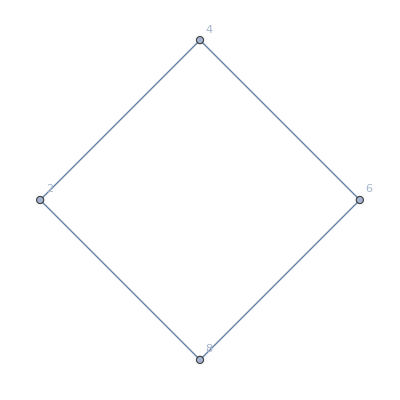

```mathematica
CycleGr[{2,4,6,8}]
```

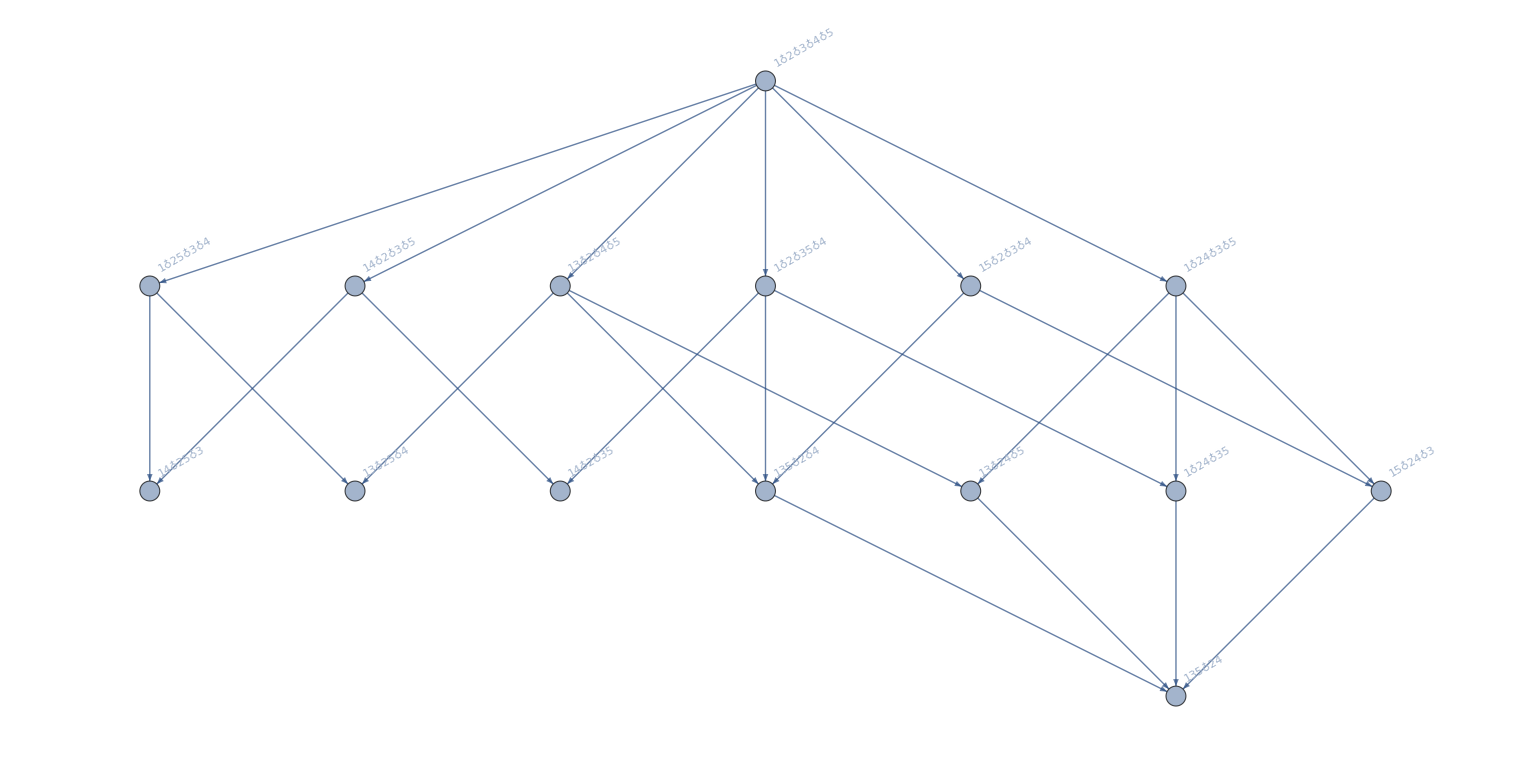

```mathematica
FindFullFormula[PathGr[5]]//FormulaGraphReverse2
```

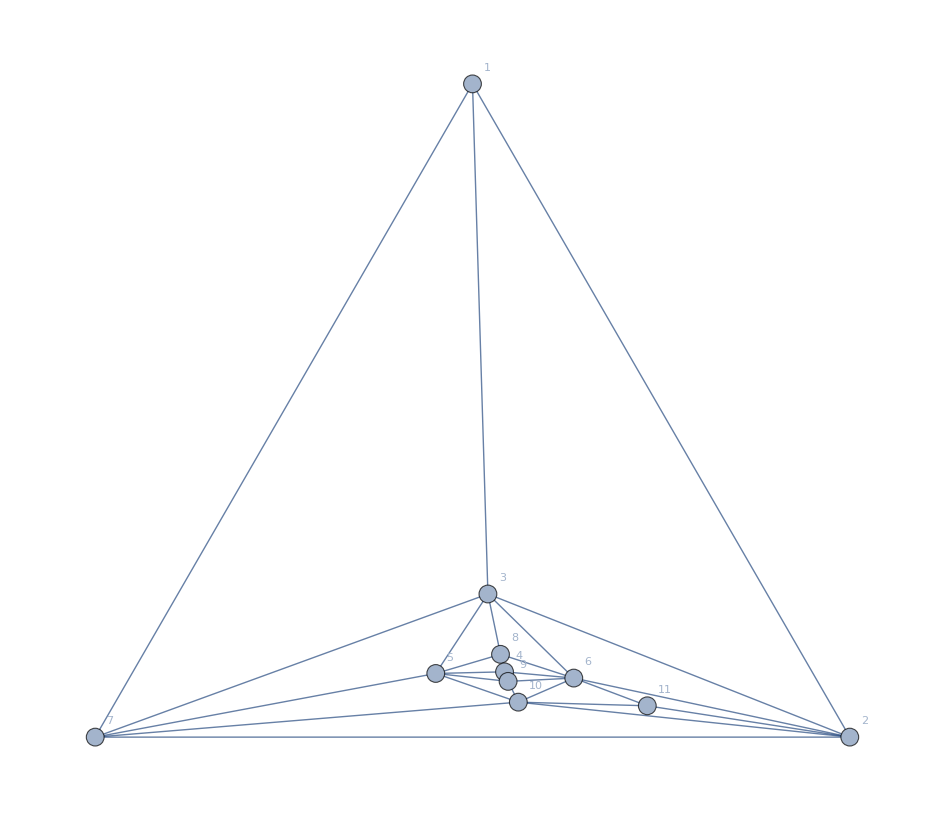

```mathematica
g=Graph[ReadGrof[900],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
ApplyToGraph[g_Graph,sets_List]:=Block[{result=g},
Table[
If[Length[bucket]≠1,
result=VertexContract[result,bucket]
],
{bucket,sets}
];
result
]
```

```mathematica
ApplyToGraph2[g_Graph,sets_List]:=With[{h=ApplyToGraph[g,sets]},
Labeled[Graph[VertexList[h],EdgeList[h],VertexLabels->"Name"],ChromaticPolynomial[h,x]]
]
```

```mathematica
MakeComplete[g_,vertices_]:=Block[{result=g},
Table[
If[!EdgeQ[result,fromto],
result=EdgeAdd[result,fromto]
],
{fromto,Map[#[[1]]<->#[[2]]&,Subsets[vertices,{2}]]}
];
Graph[VertexList[result],EdgeList[result],VertexLabels->"Name"]
]
```

```mathematica
GraphWithChrom[g_]:=Labeled[g,Style[{Factor[ChromaticPolynomial[g,x]/(x(x-1))],ChromaticPolynomial[g,4]},If[ChromaticPolynomial[g,4]!=0,Darker[Green],Red]]]
```

```mathematica
WorkOnGraph[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Column[
{GraphWithChrom[Graph[EdgeList[g],GraphHighlight->EdgeList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
TableForm[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{Rotate[SetsToLabel[sol],Pi/2],GraphWithChrom[lefta],GraphWithChrom[righta],GraphWithChrom[middlea],Rotate[Framed[Factor[(ChromaticPolynomial[lefta,x]*ChromaticPolynomial[righta,x]/ChromaticPolynomial[middlea,x])/(x(x-1))]],-Pi/2]},
{sol,sols}
]
]
}
]
]
```

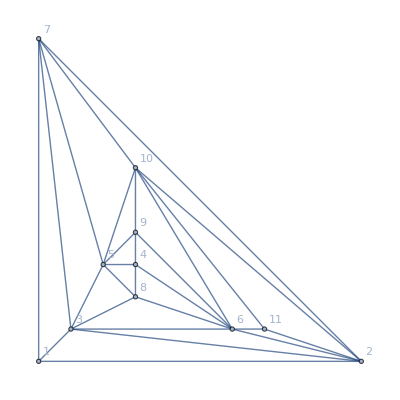
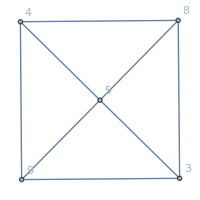
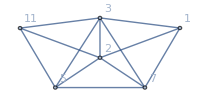
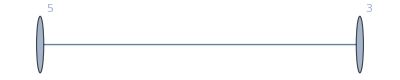
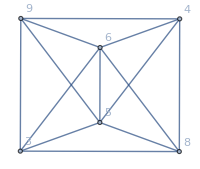
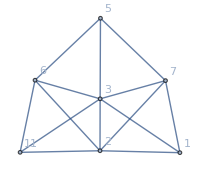
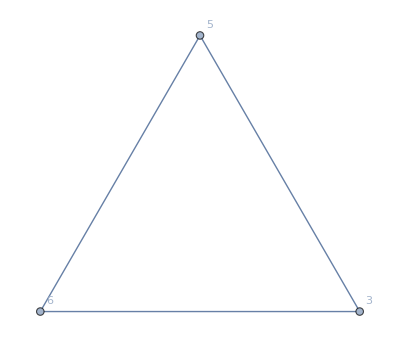
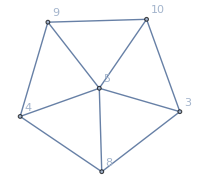
-Graphics-{(-3+x)^3 (-2+x) (-383+542 x-315 x^2+95 x^3-15 x^4+x^5),216}
3a♁56 | -Graphics-{(-2+x) (7-5 x+x^2),72} | -Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{1,12} | (-3+x)^3 (-2+x)^2 (7-5 x+x^2)
3a♁5♁6 | -Graphics-{(-3+x) (-2+x) (13-7 x+x^2),24} | -Graphics-{(-3+x)^2 (-2+x) (7-5 x+x^2),72} | -Graphics-{-2+x,24} | (-3+x)^3 (-2+x) (13-7 x+x^2) (7-5 x+x^2)
3♁56♁a | -Graphics-{(-3+x) (-2+x) (5-4 x+x^2),120} | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{-2+x,24} | (-4+x) (-3+x)^4 (-2+x) (5-4 x+x^2)
3♁5♁6♁a | -Graphics-{(-4+x) (-3+x) (-2+x) (10-6 x+x^2),0} | -Graphics-{(-3+x)^3 (-2+x) (13-7 x+x^2),24} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x)^3 (-2+x) (13-7 x+x^2) (10-6 x+x^2)

```mathematica
WorkOnGraph[g,{3,6,10,5}]
```

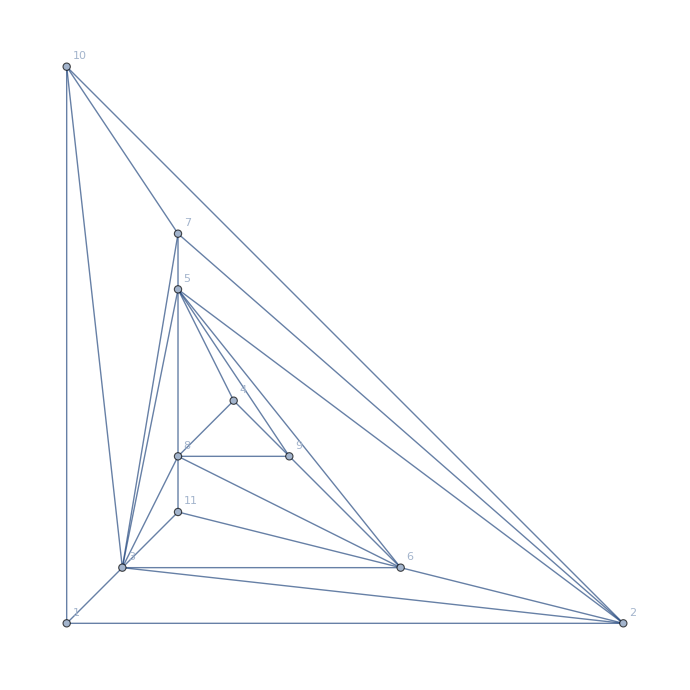

```mathematica
Graph[ReadGrof[1000],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

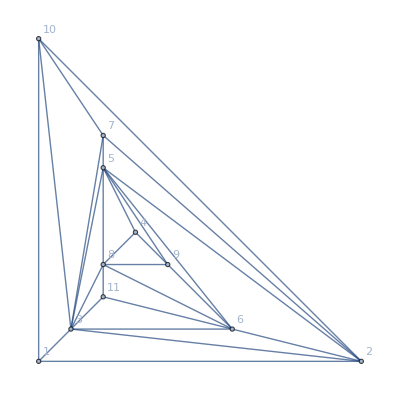
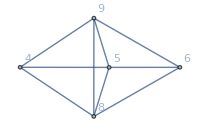
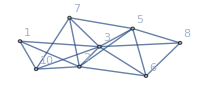
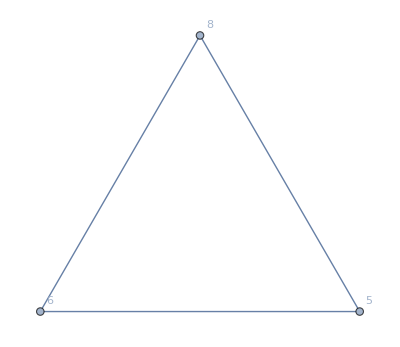
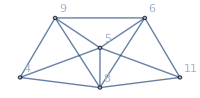
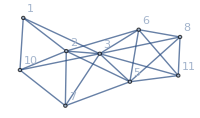
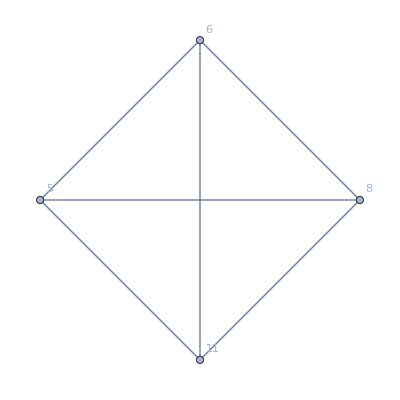
-Graphics-{(-3+x)^8 (-2+x),24}
5b♁6♁8 | -Graphics-{(-3+x)^2 (-2+x),24} | -Graphics-{(-3+x)^5 (-2+x),24} | -Graphics-{-2+x,24} | (-3+x)^7 (-2+x)
5♁6♁8♁b | -Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{(-4+x) (-3+x)^5 (-2+x),0} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x)^7 (-2+x)

```mathematica
ex2=WorkOnGraph[ReadGrof[1000],{5,6,11,8}]
```

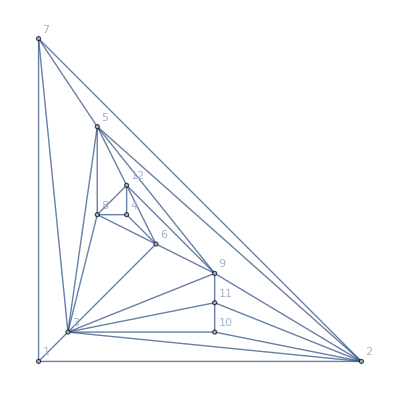

```mathematica
Graph[ReadGrof[5000],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

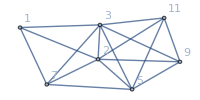
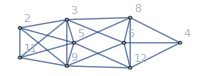
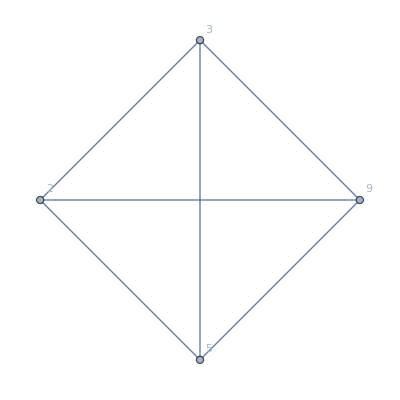
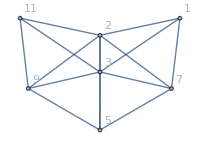
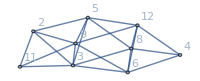
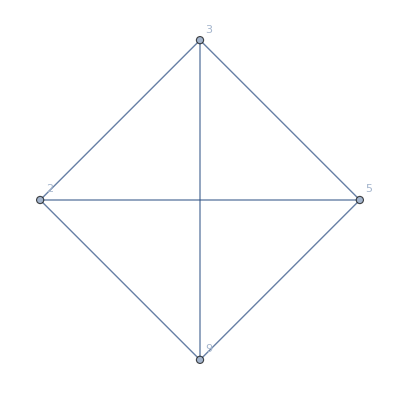
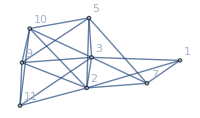
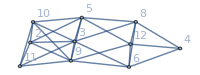
-Graphics-{(-3+x)^6 (-2+x) (-32+29 x-9 x^2+x^3),96}
2♁3♁5a♁9 | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0} | -Graphics-{(-3+x) (-2+x),24} | (-4+x)^2 (-3+x)^4 (-2+x) (-32+29 x-9 x^2+x^3)
2♁3♁5♁9a | -Graphics-{(-3+x)^4 (-2+x),24} | -Graphics-{(-3+x)^3 (-2+x) (-32+29 x-9 x^2+x^3),96} | -Graphics-{(-3+x) (-2+x),24} | (-3+x)^6 (-2+x) (-32+29 x-9 x^2+x^3)
2♁3♁5♁9♁a | -Graphics-{(-4+x)^2 (-3+x)^3 (-2+x),0} | -Graphics-{(-4+x)^2 (-3+x)^2 (-2+x) (-32+29 x-9 x^2+x^3),0} | -Graphics-{(-4+x) (-3+x) (-2+x),0} | (-4+x)^3 (-3+x)^4 (-2+x) (-32+29 x-9 x^2+x^3)

```mathematica
ex2=WorkOnGraph[ReadGrof[5000],{5,9,2,10,3}]
```

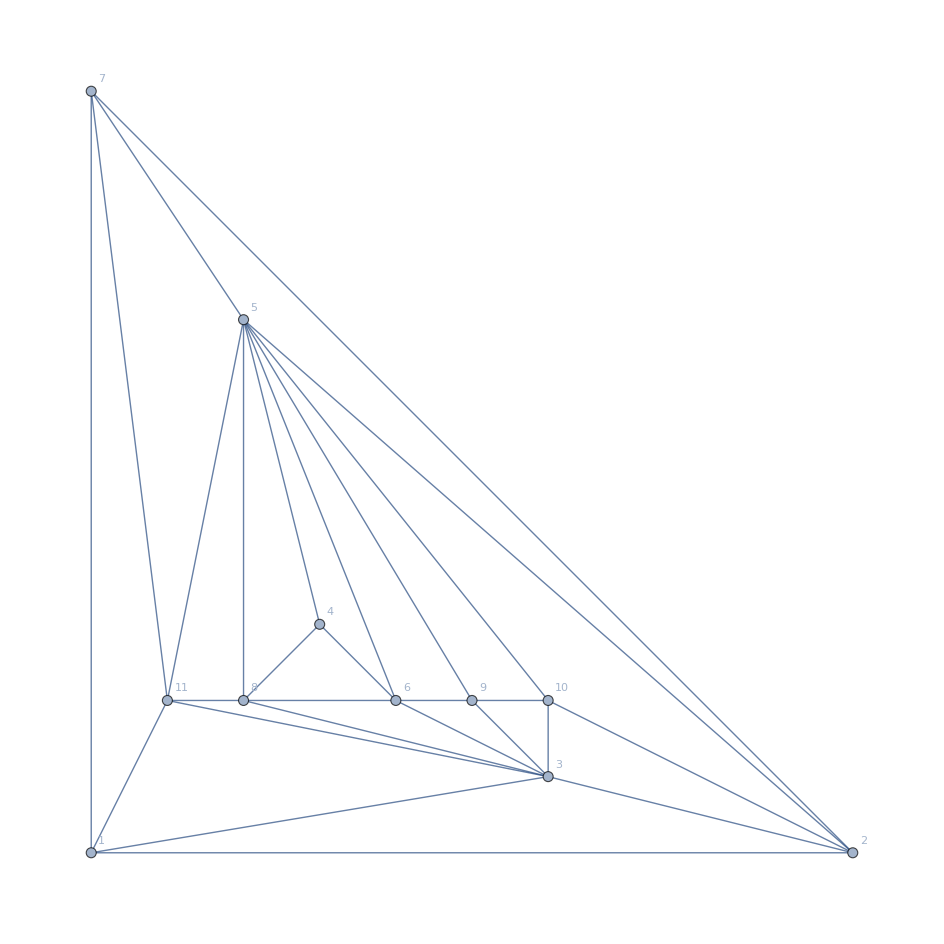

```mathematica
Graph[ReadGrof[500],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

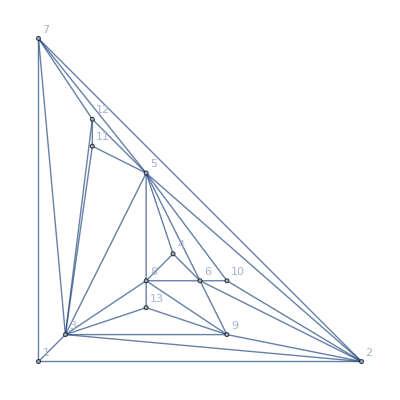
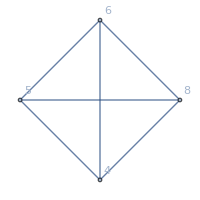
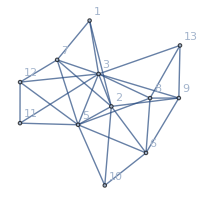
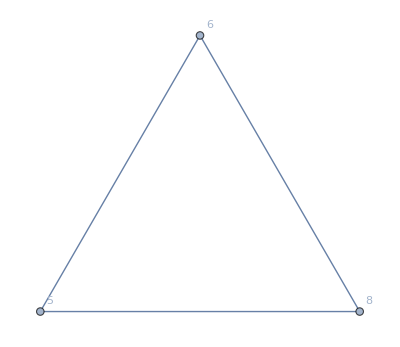
-Graphics-{(-3+x)^7 (-2+x) (-32+29 x-9 x^2+x^3),96}
5♁6♁8 | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x)^6 (-2+x) (-32+29 x-9 x^2+x^3),96} | -Graphics-{-2+x,24} | (-3+x)^7 (-2+x) (-32+29 x-9 x^2+x^3)

```mathematica
ex2=WorkOnGraph[ReadGrof[50000],{5,6,8}]
```

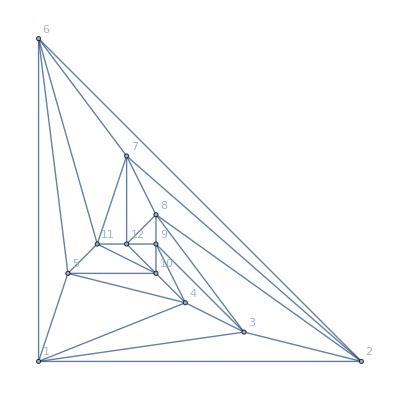

```mathematica
Graph[plantri[[1]],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

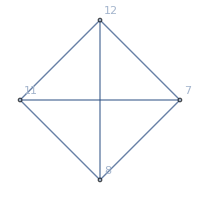
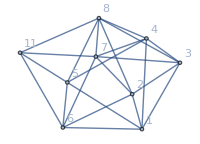
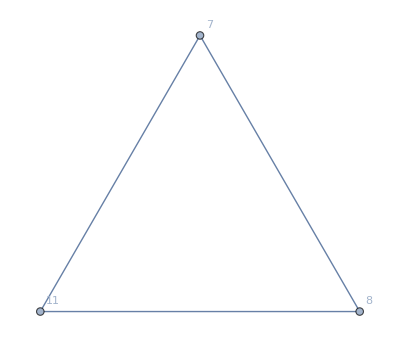
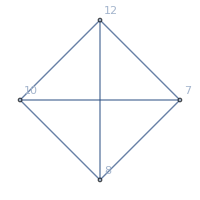
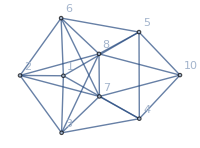
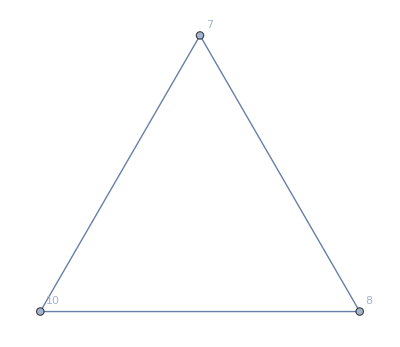
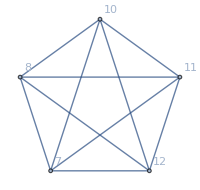
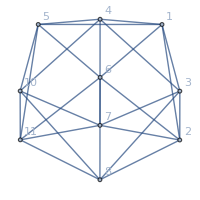
-Graphics-{(-3+x) (-2+x) (20170-40240 x+36408 x^2-19698 x^3+6999 x^4-1670 x^5+260 x^6-24 x^7+x^8),240}
79♁8a♁b | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48} | -Graphics-{-2+x,24} | (-3+x)^2 (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5)
79♁8b♁a | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48} | -Graphics-{-2+x,24} | (-3+x)^2 (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5)
79♁8♁a♁b | -Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6)
7a♁8b♁9 | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48} | -Graphics-{-2+x,24} | (-3+x)^2 (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5)
7a♁8♁9b | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48} | -Graphics-{-2+x,24} | (-3+x)^2 (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5)
7a♁8♁9♁b | -Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6)
7♁8a♁9b | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{(-3+x) (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5),48} | -Graphics-{-2+x,24} | (-3+x)^2 (-2+x) (-742+910 x-461 x^2+122 x^3-17 x^4+x^5)
7♁8a♁9♁b | -Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6)
7♁8b♁9♁a | -Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6)
7♁8♁9b♁a | -Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6),48} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x) (-2+x) (2678-3877 x+2426 x^2-846 x^3+174 x^4-20 x^5+x^6)
7♁8♁9♁a♁b | -Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} | -Graphics-{(-4+x) (-3+x) (-2+x) (3130-4282 x+2559 x^2-865 x^3+175 x^4-20 x^5+x^6),0} | -Graphics-{(-4+x) (-3+x) (-2+x),0} | (-5+x) (-4+x) (-3+x) (-2+x) (3130-4282 x+2559 x^2-865 x^3+175 x^4-20 x^5+x^6)

```mathematica
WorkOnGraph[Graph[plantri[[1]],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],{7,8,9,10,11}]
```